```mathematica
(*
Práctica 2 parte 1
Alumnos:
Dan Anitei
Vicente Gras Mas

*)

(*Cálculo de t configuraciones de un autómata celular Inicial y una Regla*)
```

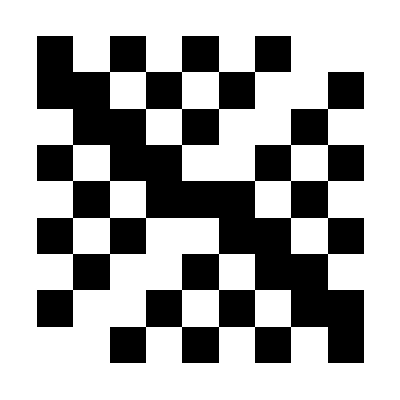

```mathematica
AC[Inicial_List,Regla_Integer,t_Integer]:=Module[{ReglaR,i,estado,configFinal},
estado = Inicial;
(*Convertir la regla en una lista de listas*)
ReglaR = Factorizar[Regla];
configFinal = {};
(*Append del estado inicial a la solución final*)
AppendTo[configFinal,estado];
(*Tantas iteraciones de configuraciones como t tengamos*)
For[i = 1,i≤t+1,i++,
estado = SiguienteConfig[ReglaR,estado];
AppendTo[configFinal,estado];
];

ArrayPlot[configFinal]
]

(*Cálculo de la siguiente configuracion dado un Estado y una Regla*)

SiguienteConfig[Regla_List,Estado_List]:=Module[{regla,estado,i,listaVecinos,ultimo},
regla = Regla;
estado = Estado;
listaVecinos = {};
(*último elemento del estado*)
ultimo = Length[estado];
For[i = 1,i≤Length[estado],i++,
(*Ambos if cubren el caso de los vecinos del primer y último elemento 
(hacen la lista circular)*)
If[i == 1,
estado[[1]]=Vecino[Regla,{estado[[ultimo]],estado[[1]],estado[[2]]}];
Continue[];
];
If[i == ultimo,
estado[[ultimo]]=Vecino[Regla,{estado[[ultimo-1]],estado[[ultimo]],estado[[1]]}];
Continue[];
];
estado[[i]]= Vecino[Regla,{estado[[i-1]],estado[[i]],estado[[i+1]]}];
];

Return[estado];

]

(*Cálculo del estado de una célula dados sus vecinos*)

Vecino[Regla_List,Vecinos_List]:=Module[{vecinos,ret},
vecinos = Vecinos;
(*Hacemos append de _ para tener un estado con cualquier valor*)
AppendTo[vecinos,_];
(*Buscamos dicho valor anteriormente*)
ret = Cases[Regla,vecinos];
Return[ret[[1,4]]];

]

(*Cálculo de la Regla a una lista de listas*)

Factorizar[Regla_Integer]:=Module[{num,factorizacion,estados,cntEstados,est},
num = Regla;
estados = {{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}};
cntEstados = 1;
(*dividiremos el número regla para obtener su valor en binario*)
While[num>0,

AppendTo[estados[[cntEstados]],Mod[num,2]];
num = Floor[num/2];
cntEstados = cntEstados + 1;

];
(*Rellenaremos los siguientes estados con 0 para mantener la concordancia 
de la lista de listas estados(todas las listas dentro de la lista estados tienen 4 elementos)*)
While[cntEstados < 9,
AppendTo[estados[[cntEstados]],0];
cntEstados = cntEstados + 1;
];
Return[estados];

]
AC[{1,0,1,0,1,0,1,1,0},54,7]
```